# Numerical Functions

## Reducing Numerical Error

### Avoid incomplete mantissa

```mathematica
(*Introducir al menos 16 dígitos*)
pi1=3.14159;
pi2=N[Pi];
```

```mathematica
Abs[pi1-pi2]/Abs[pi2]
```

8.44664×10^-7

### Diagnose catastrophic cancellation

```mathematica
{x1,x2}=SolveValues[a x^2+b x+c==0,x]
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

#### Case: b^2>>4ac and b>0

```mathematica
radical=(-b-√(b^2-4a c))
```

-b-√(b^2-4 a c)

```mathematica
Expand[x2*radical]/radical
```

(2 c)/(-b-√(b^2-4 a c))

### Reducing amount of operations

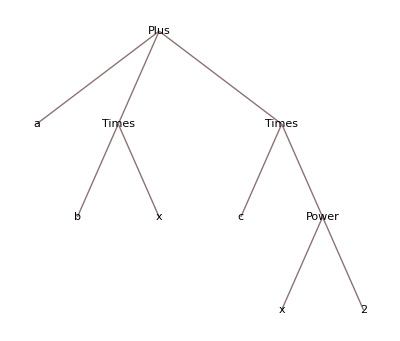

```mathematica
a+b x+c x^2//TreeForm
```

a+x (b+x (c+d x))

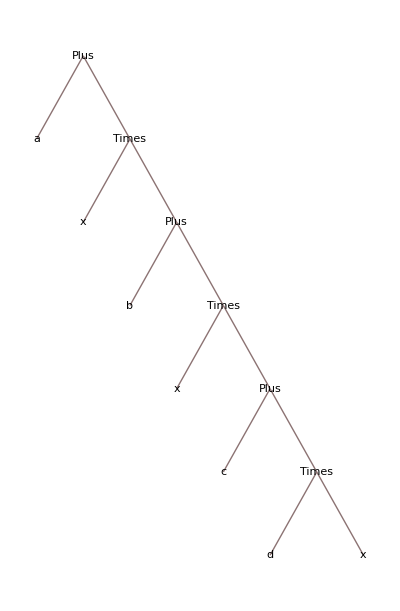

```mathematica
Echo@HornerForm[a+b x+c x^2+d x^3,x]//TreeForm
```

### Overflow/Underflow

#### Rescale, change units

WolframAlphaQueryParseResults

h

```mathematica
UnitConvert[N[Quantity[, "PlanckConstant"]]]
```

6.62607×10^-34 kg m^2/s

```mathematica
h=QuantityMagnitude[%]
```

6.62607×10^-34

```mathematica
h^10
```

General::munfl: (6.62607×10^-34)^10 is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
$MinMachineNumber
```

2.22507×10^-308

#### Math functions

```mathematica
Log[Gamma[10.^100]]
```

General::ovfl: Overflow occurred in computation.

Overflow[]

```mathematica
LogGamma[10.^100]
```

2.29259×10^102

## Testing new functions

### Acceleration of Gravity

```mathematica
{𝒢,N[𝒢]}
```

{𝒢,9.8 m/s^2}

```mathematica
Dt[x0+v0 t+1/2 𝒢 t^2,t]
```

v0+t 𝒢+t Dt[v0,t]+Dt[x0,t]

```mathematica
Quantity[2,"Seconds"]
```

2 s

```mathematica
With[{x0=Quantity[1, "Meters"],v0=Quantity[2, ("Meters")/("Seconds")],t=Quantity[2, "Seconds"]},x0+v0 t+1/2 𝒢 t^2//N]
```

24.6 m

### Binomial Coefficient

```mathematica
binomialCoefficient[5000.,23]//IntegerPart
```

definition 1

438336194813346939571665254903928997495886316751785513707372544

```mathematica
binomialCoefficient[5000,23]
```

definition 2

438336194813347030686327212581618135759251704725705742383560000

```mathematica
binomialCoefficient[√5,3.]
```

binomialCoefficient[√5,3.]

```mathematica
N[binomialCoefficient[√5,3]]
```

definition 1

0.108746

```mathematica
FunctionExpand[binomialCoefficient[5.,3.]]//FullSimplify
```

definition 3

10.

### Ramanujan Formula for Pi

```mathematica
(*try: 100, 1*)
piR=ramanujanPi[100];
piM=N[Pi];
```

```mathematica
Abs[piR-piM]/Abs[piM]
```

1.41358×10^-16

```mathematica
(*try: 100, 4*)
piR=ramanujanPi[100,40];
piM=N[Pi,40];
```

```mathematica
Abs[piR-piM]/Abs[piM]
```

0.

### Sqrt Heron' s Algorithm

```mathematica
heronSqrt[0.]
```

0.

```mathematica
heronSqrt[2.]//InputForm
```

1.5

1.4166666666666665

1.4142156862745097

1.4142135623746899

1.414213562373095

1.414213562373095

1.414213562373095

```mathematica
√2.//InputForm
```

1.4142135623730951

```mathematica
heronSqrt[2.*10^-20]//InputForm
```

0.5

0.25

0.125

0.0625

0.03125

0.015625

0.0078125

0.003906250000000001

0.001953125000000003

0.0009765625000000067

0.0004882812500000136

0.00024414062500002727

0.0001220703125000546

0.00006103515625010922

0.00003051757812521845

0.000015258789062936906

7.629394532123813*^-6

3.814697267372626*^-6

1.907348636307753*^-6

9.536743233967566*^-7

4.768371721841382*^-7

2.3841860706358847*^-7

1.192093454748293*^-7

5.96047566234553*^-8

2.980254608357283*^-8

1.490160858358784*^-8

7.451475360285884*^-9

3.727079696256059*^-9

1.86622291391008*^-9

9.384698736401338*^-10

4.798905798842519*^-10

2.6078337349528086*^-10

1.6873768966174476*^-10

1.4363242737752343*^-10

1.4143837480225457*^-10

1.4142135726118847*^-10

1.414213562373095*^-10

1.414213562373095*^-10

1.414213562373095*^-10

```mathematica
heronSqrt[2.*10^-20,10^-10]//InputForm
```

1.5*^-10

1.4166666666666667*^-10

1.4142156862745097*^-10

1.4142135623746897*^-10

1.414213562373095*^-10

1.414213562373095*^-10

1.414213562373095*^-10

```mathematica
heronSqrt[2.*10^-20,10^-10,PrecisionGoal->3]//InputForm
```

1.5*^-10

1.4166666666666667*^-10

1.4142156862745097*^-10

1.4142135623746897*^-10

1.4142135623746897*^-10

### Solution of the quadratic Equation

```mathematica
quadraticSolve[0,0,0]
```

quadraticSolve::allsol: this equation doesn't have a unique solution

{}

```mathematica
quadraticSolve[0,0,1]
```

quadraticSolve::nosol: this equation doesn't have any solutions

{}

```mathematica
quadraticSolve[0,2,1]
```

quadraticSolve::lineq: this is a linear equation

{-0.5}

```mathematica
quadraticSolve[1,2,1]
```

{-1.,-1.}

```mathematica
quadraticSolve[1,1,1]
```

quadraticSolve::complex: this equation has complex solutions

{-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ}

```mathematica
quadraticSolve[1,10.^50,6]
```

{-1.×10^50,-6.×10^-50}

# Pregunta 4

```mathematica
struveH[7/2,-2]
```

1/π+BesselY[7/2,-2]

```mathematica
BesselY
```

```mathematica
BesselY[7/2,2.5]
```

-1.00497

```mathematica
Gamma
```

```mathematica
struveH[5/2,-1.]
```

0.31831+2.87639 ⅈ

```mathematica
(-24.243/3.)^(-1/2)
```

0.-0.351777 ⅈ

```mathematica
StruveH[1/2,0.]
```

0.

```mathematica
Im[StruveH[-7/2,100.]]
```

0

```mathematica
Sqrt[]
```